```mathematica
Tau = 2 Pi;
Second[lst_]:=lst[[2]];
Middle[xs_]:=xs[[Floor[(Length[xs]+1)/2]]];
WithXRegion[a_,b_][xs_]:=Block[{n=Length[xs]},Table[{a + (b-a) i/n, xs[[i]]},{i,1,n}]];
SimpsonSum[xs_]:=Block[{n=Length[xs]},
xs[[1]] + 4Sum[xs[[j]], {j, 2, n-1, 2}] + 2Sum[xs[[j]],{j,3,n-1,2}]+xs[[n]]
];

PredictedPressure[a_,w_]:=-Zeta[3]/(8 Tau) Exp[-a w];
Exact[a_]:=-Zeta[3]/(4 Tau a^3)//N;
ParallelPlates[a_,L_,w_, n_:Automatic ]:=Module[{r,s, le, e,da,v,d,q,  P,idx,rhs,eqs,vars,sol},
If[n==Automatic,n=Max[30,10L/a // Ceiling]];
If[w==0,Return[Table[0,n]]];
r=L/n;
idx=Floor[n/2];
s[i_]:=(i-0.5)/n;
d[i_,j_]:=r(i-j);
le[ds_]:=Sqrt[a^2 + L^2 ds^2];

e[i_,j_]:=-a w/Tau BesselK[1,w le[(i-j)/n]] / le[(i-j)/n]//N;
q[i_,j_][t_]:= -2a w/Tau^2 (BesselK[1,w le[s[i]-t]]/le[s[i]-t]) BesselK[0,w L Abs[s[j]-t]];
da[i_,j_,k_]:=
Piecewise[{
{(EulerGamma - 1 - Log[n w L])/Tau,Abs[k-j]/n == 0}
(*{ L NIntegrate[q[i,j][t],{t,(k-1)/n,k/n}] , Abs[k-j]/n≤ 0.01}*)
},L/n q[i,j][s[k]]]//Re;
v[i_,j_]:=-1/Tau BesselK[0, w Sqrt[a^2 + d[i,j]^2]]+Sum[da[i,j,k],{k,1,n}]//N;

rhs[0,i_]:=-r Sum[e[k,i] P[1,k],{k,1,n}];
rhs[1,i_]:=-r Sum[e[k,i] P[0,k],{k,1,n}]+v[i,idx];
eqs = Table[1/2 P[b,i]==rhs[b,i], {b,0,1},{i,1,n}]//Flatten;
vars=Table[P[b,i],{b,0,1},{i,1,n}]//Flatten;

sol= NSolve[eqs,vars]//First;
w^2 /Tau (Table[P[0,i]/.sol,{i,1,n}])
];


Pressure[a_,L_,w_]:=ParallelPlates[a,L,w]//Middle;

Force[a_,L_]:=Module[{integrand, ubound, dx, n, x,result},
integrand[w_]:=Pressure[a,L,w];
n = 50;
ubound=20 Exp[-a];
dx = ubound/n//N;
x=Monitor[Table[integrand[ubound * j/n],{j,1,n}],ProgressIndicator[j/n//N,{0,1}]];
result = dx/3 * SimpsonSum[x];
If[Abs[Last[x]/result]>0.01,Print["Possibly insufficient integral bound"]];
If[Abs[Last[x]/result]<0.00001, Print["Possibly too large integral bound"]];
result
];
```

```mathematica
ParallelPlates[1,20,4]
```

Set::wrsym: Symbol Automatic is Protected.

Table::iterb: Iterator {i,1,Automatic} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

First::nofirst: {} has zero length and no first element.

(8 Table[P$10908[0,i]/.sol$10908,{i,1,Automatic}])/π

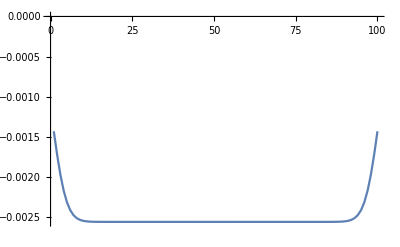

```mathematica
Block[{pts=ParallelPlates[2,20,4,100]},
ListLinePlot[{pts},PlotRange->{All,0}]
]
```

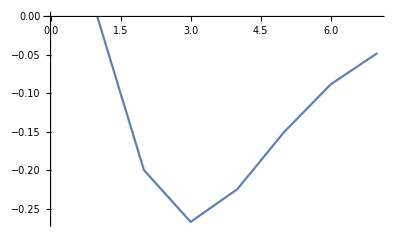

```mathematica
Table[Pressure[1,20,w],{w,0,6,1}]//ListLinePlot
```

```mathematica
Force[2,10]
```

Possibly insufficient integral bound

-0.0450984

```mathematica
-0.11075113212725819
```

-0.110751

```mathematica
%/Exact[2]
```

18.5248

```mathematica
Block[{f=Force[3,20]}, {f, Exact[3], f/Exact[3]}]
```

Possibly too large integral bound

{-0.0293507,-0.00177142,16.569}

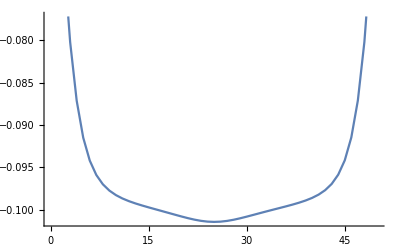

```mathematica
%//ListLinePlot
```

```mathematica
Module[{a,L,w,n,r,s,ld,le,da,q,result},
a=0.1;
L=10;
w=1;
n=200;
r=L/n;
ld[ds_]:=L Abs[ds];
le[ds_]:=Sqrt[a^2+L^2ds^2];
s[i_]:=(i-1/2)/n;
q[i_,j_][t_]:= -2a w/Tau^2 (BesselK[1,w le[s[i]-t]]/le[s[i]-t]) BesselK[0,w ld[s[j]-t]];
da[i_,j_,k_]:=
Piecewise[{
(*{(a w/Tau BesselK[1,w le[s[i]-s[k]]]/le[s[i]-s[k]])(EulerGamma - 1 - Log[n w L])/Tau,Abs[k-j]/n == 0},*)
{ L NIntegrate[q[i,j][t],{t,(k-1)/n,k/n}] , Abs[k-j]/n≤ 0.1}
},L/n q[i,j][s[k]]]//Re;

result=Table[da[n/5,n/2,k],{k,1,n}];
Print[{Sum[p,{p,result}],NIntegrate[q[n/5,n/2][t],{t,0,1}]}];
Return[result];
];
```

{-0.00551787,-0.000551782+1.83283×10^-22 ⅈ}

Return[{-7.53137×10^-8,-8.72459×10^-8,-1.01193×10^-7,-1.17522×10^-7,-1.36673×10^-7,-1.59176×10^-7,-1.85669×10^-7,-2.16926×10^-7,-2.53885×10^-7,-2.97691×10^-7,-3.49747×10^-7,-4.11775×10^-7,-4.85907×10^-7,-5.74786×10^-7,-6.81716×10^-7,-8.10847×10^-7,-9.67423×10^-7,-1.15813×10^-6,-1.39153×10^-6,-1.67874×10^-6,-2.03426×10^-6,-2.47723×10^-6,-3.03323×10^-6,-3.73686×10^-6,-4.63561×10^-6,-5.79573×10^-6,-7.31129×10^-6,-9.31876×10^-6,-0.0000120208,-0.0000157266,-0.0000209234,-0.0000284068,-0.0000395334,-0.0000567325,-0.0000846014,-0.000132348,-0.00021911,-0.00038193,-0.000652796,-0.000867101,-0.00073279,-0.000481273,-0.000309943,-0.000210164,-0.000150819,-0.000113544,-0.000088832,-0.000071668,-0.0000592736,-0.0000500292,-0.0000429452,-0.0000373915,-0.0000329524,-0.0000293445,-0.0000263696,-0.0000238858,-0.0000217889,-0.0000200014,-0.0000184645,-0.000017133,-0.0000159714,-0.0000149519,-0.0000140522,-0.0000132544,-0.0000125438,-0.0000119085,-0.0000113386,-0.0000108258,-0.0000103633,-9.94522×10^-6,-9.5667×10^-6,-9.22359×10^-6,-8.91237×10^-6,-8.63003×10^-6,-8.37404×10^-6,-8.14221×10^-6,-7.93273×10^-6,-7.74407×10^-6,-7.57496×10^-6,-7.42514×10^-6,-7.29233×10^-6,-7.17676×10^-6,-7.07813×10^-6,-6.99637×10^-6,-6.93171×10^-6,-6.88468×10^-6,-6.8562×10^-6,-6.84766×10^-6,-6.86108×10^-6,-6.89935×10^-6,-6.96652×10^-6,-7.06846×10^-6,-7.21377×10^-6,-7.41558×10^-6,-7.69508×10^-6,-8.08907×10^-6,-8.6695×10^-6,-9.60702×10^-6,-0.0000115166,-0.0000162542,-9.92407×10^-6,-7.09172×10^-6,-5.48769×10^-6,-4.39139×10^-6,-3.58275×10^-6,-2.96078×10^-6,-2.4695×10^-6,-2.07429×10^-6,-1.75207×10^-6,-1.48665×10^-6,-1.26624×10^-6,-1.082×10^-6,-9.27155×10^-7,-7.96419×10^-7,-6.85602×10^-7,-5.91348×10^-7,-5.10943×10^-7,-4.42169×10^-7,-3.83205×10^-7,-3.32545×10^-7,-2.88685×10^-7,-2.51115×10^-7,-2.18664×10^-7,-1.90594×10^-7,-1.6628×10^-7,-1.45193×10^-7,-1.26883×10^-7,-1.10968×10^-7,-9.71192×10^-8,-8.50575×10^-8,-7.45425×10^-8,-6.53682×10^-8,-5.73571×10^-8,-5.03563×10^-8,-4.4234×10^-8,-3.88762×10^-8,-3.41845×10^-8,-3.00733×10^-8,-2.64687×10^-8,-2.33065×10^-8,-2.05309×10^-8,-1.80932×10^-8,-1.59513×10^-8,-1.40683×10^-8,-1.24122×10^-8,-1.0955×10^-8,-9.67216×10^-9,-8.54245×10^-9,-7.54714×10^-9,-6.6699×10^-9,-5.89644×10^-9,-5.21422×10^-9,-4.61227×10^-9,-4.08095×10^-9,-3.61183×10^-9,-3.19749×10^-9,-2.83141×10^-9,-2.50787×10^-9,-2.22186×10^-9,-1.96893×10^-9,-1.7452×10^-9,-1.54725×10^-9,-1.37206×10^-9,-1.21697×10^-9,-1.07964×10^-9,-9.58×10^-10,-8.50241×10^-10,-7.54752×10^-10,-6.70118×10^-10,-5.95087×10^-10,-5.28555×10^-10,-4.69547×10^-10,-4.17201×10^-10,-3.70755×10^-10,-3.29536×10^-10,-2.92949×10^-10,-2.60467×10^-10,-2.31623×10^-10,-2.06006×10^-10,-1.83251×10^-10,-1.63033×10^-10,-1.45068×10^-10,-1.29102×10^-10,-1.14909×10^-10,-1.02291×10^-10,-9.10711×10^-11,-8.10929×10^-11,-7.22176×10^-11,-6.43221×10^-11,-5.72972×10^-11,-5.1046×10^-11,-4.54824×10^-11,-4.05302×10^-11,-3.61216×10^-11,-3.21963×10^-11,-2.8701×10^-11,-2.5588×10^-11,-2.28153×10^-11,-2.03452×10^-11,-1.81446×10^-11}]

```mathematica
Force[3,30]
```

Part::partd: Part specification $Aborted⟦1⟧ is longer than depth of object.

Last::normal: Nonatomic expression expected at position 1 in Last[$Aborted].

0.04 (Symbol+$Aborted⟦1⟧)

```mathematica
Exact[3]
```

-0.00177142

```mathematica
Force[3,30] (*n=50*)
```

-0.000443263

-3.54644×10^-6

-0.000140758

```mathematica
Exact[3]
```

-0.00177142

```mathematica
Exact[2]
```

-0.00597854

```mathematica
Exact[1]
```

-0.0478283

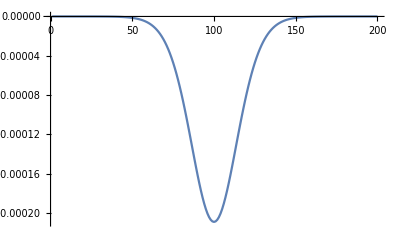

```mathematica
ParallelPlates[1,10,4]//ListLinePlot[#,PlotRange->All]&
```

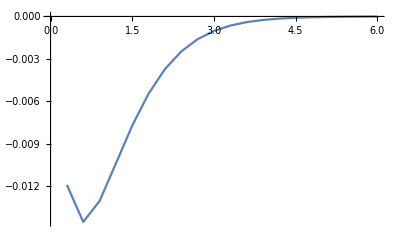

```mathematica
Table[{w,Pressure[1,10][w]},{w,0,6,0.3}]//ListLinePlot
```

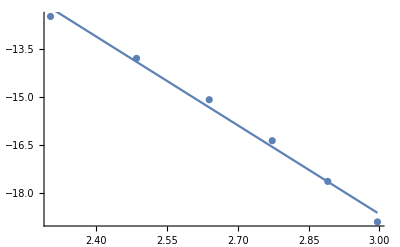
{-Graphics-,-9.27579,R^2 = 0.991057}

```mathematica
TestPowerDependency[Force[#,15#]&,10,20,5]
```

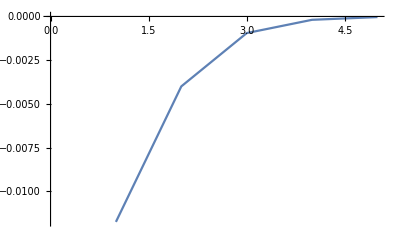

```mathematica
Table[Pressure[1,20,w],{w,1,5}]//ListLinePlot
```

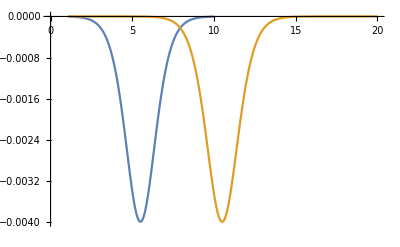

```mathematica
{ParallelPlates[1, 10, 2]//ScaleToRegion[1,10],ParallelPlates[1,20,2]//ScaleToRegion[1,20]}//ListLinePlot
```

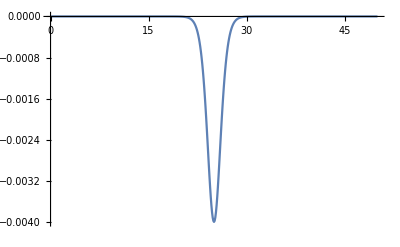

```mathematica
Block[{pts=ParallelPlates[1,50,2]//WithXRegion[0,50]},
Show[ListLinePlot[pts,PlotRange->All],ListLinePlot[Table[Middle[pts],{i,1,Length[pts]}]]]
]
```

```mathematica
lsts = ParallelTable[Force[a,20],{a,1,2.5,0.5}];
```

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

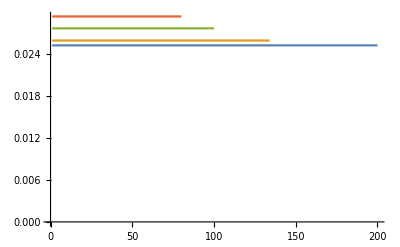

```mathematica
exacts = Table[Table[Exact[1+(n-1)*0.5] / Middle[lsts[[n]]],Length[lsts[[n]]]],{n,1,Length[lsts]}];
ListLinePlot[exacts,PlotRange->{0,All}]
```

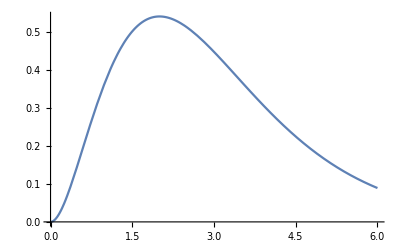

```mathematica
Plot[x^2 Exp[-x], {x,0,6}]
```

```mathematica
Integrate[x^2 Exp[-a x],{x,0,Infinity}]
```

ConditionalExpression[2/a^3,Re[a]>0]